```mathematica
EQ1= (r^2-p^2)D[U[ξ],{ξ,2}] -g^2 l^2 U[ξ] V[ξ]^2
```

-g^2 l^2 U[ξ] V[ξ]^2+(-p^2+r^2) U''[ξ]

```mathematica
EQ2= (r^2-p^2)D[V[ξ],{ξ,2}] -g^2 k^2 V[ξ] U[ξ]^2
```

-g^2 k^2 U[ξ]^2 V[ξ]+(-p^2+r^2) V''[ξ]

## Coth-Cosech method

```mathematica
U[ξ_]= a0 +a1 Coth[I ξ]+b1 Csch[I ξ]
```

a0-ⅈ a1 Cot[ξ]-ⅈ b1 Csc[ξ]

```mathematica
V[ξ_]= A0 +A1 Coth[I ξ] + B1 Csch[I ξ]
```

A0-ⅈ A1 Cot[ξ]-ⅈ B1 Csc[ξ]

```mathematica
EQ1
```

-g^2 l^2 (a0-ⅈ a1 Cot[ξ]-ⅈ b1 Csc[ξ]) (A0-ⅈ A1 Cot[ξ]-ⅈ B1 Csc[ξ])^2+(-p^2+r^2) (-ⅈ b1 Cot[ξ]^2 Csc[ξ]-2 ⅈ a1 Cot[ξ] Csc[ξ]^2-ⅈ b1 Csc[ξ]^3)

```mathematica
EQ11=Expand[-g^2 l^2 (a0-ⅈ a1 Cot[ξ]-ⅈ b1 Csc[ξ]) (A0-ⅈ A1 Cot[ξ]-ⅈ B1 Csc[ξ])^2+(-p^2+r^2) (-ⅈ b1 Cot[ξ]^2 Csc[ξ]-2 ⅈ a1 Cot[ξ] Csc[ξ]^2-ⅈ b1 Csc[ξ]^3)]
```

-a0 A0^2 g^2 l^2+ⅈ A0^2 a1 g^2 l^2 Cot[ξ]+2 ⅈ a0 A0 A1 g^2 l^2 Cot[ξ]+2 A0 a1 A1 g^2 l^2 Cot[ξ]^2+a0 A1^2 g^2 l^2 Cot[ξ]^2-ⅈ a1 A1^2 g^2 l^2 Cot[ξ]^3+ⅈ A0^2 b1 g^2 l^2 Csc[ξ]+2 ⅈ a0 A0 B1 g^2 l^2 Csc[ξ]+2 A0 A1 b1 g^2 l^2 Cot[ξ] Csc[ξ]+2 A0 a1 B1 g^2 l^2 Cot[ξ] Csc[ξ]+2 a0 A1 B1 g^2 l^2 Cot[ξ] Csc[ξ]-ⅈ A1^2 b1 g^2 l^2 Cot[ξ]^2 Csc[ξ]-2 ⅈ a1 A1 B1 g^2 l^2 Cot[ξ]^2 Csc[ξ]+ⅈ b1 p^2 Cot[ξ]^2 Csc[ξ]-ⅈ b1 r^2 Cot[ξ]^2 Csc[ξ]+2 A0 b1 B1 g^2 l^2 Csc[ξ]^2+a0 B1^2 g^2 l^2 Csc[ξ]^2-2 ⅈ A1 b1 B1 g^2 l^2 Cot[ξ] Csc[ξ]^2-ⅈ a1 B1^2 g^2 l^2 Cot[ξ] Csc[ξ]^2+2 ⅈ a1 p^2 Cot[ξ] Csc[ξ]^2-2 ⅈ a1 r^2 Cot[ξ] Csc[ξ]^2-ⅈ b1 B1^2 g^2 l^2 Csc[ξ]^3+ⅈ b1 p^2 Csc[ξ]^3-ⅈ b1 r^2 Csc[ξ]^3

```mathematica
Collect[EQ11,{Cot[ξ],Cot[ξ]^2,Cot[ξ]^3,Csc[ξ],Cot[ξ] Csc[ξ], Cot[ξ]^2 Csc[ξ],Csc[ξ]^2,Cot[ξ] Csc[ξ]^2,Csc[ξ]^3}]
```

-a0 A0^2 g^2 l^2+(ⅈ A0^2 a1 g^2 l^2+2 ⅈ a0 A0 A1 g^2 l^2) Cot[ξ]+(2 A0 a1 A1 g^2 l^2+a0 A1^2 g^2 l^2) Cot[ξ]^2-ⅈ a1 A1^2 g^2 l^2 Cot[ξ]^3+(ⅈ A0^2 b1 g^2 l^2+2 ⅈ a0 A0 B1 g^2 l^2) Csc[ξ]+(2 A0 A1 b1 g^2 l^2+2 A0 a1 B1 g^2 l^2+2 a0 A1 B1 g^2 l^2) Cot[ξ] Csc[ξ]+(-ⅈ A1^2 b1 g^2 l^2-2 ⅈ a1 A1 B1 g^2 l^2+ⅈ b1 p^2-ⅈ b1 r^2) Cot[ξ]^2 Csc[ξ]+(2 A0 b1 B1 g^2 l^2+a0 B1^2 g^2 l^2) Csc[ξ]^2+(-2 ⅈ A1 b1 B1 g^2 l^2-ⅈ a1 B1^2 g^2 l^2+2 ⅈ a1 p^2-2 ⅈ a1 r^2) Cot[ξ] Csc[ξ]^2+(-ⅈ b1 B1^2 g^2 l^2+ⅈ b1 p^2-ⅈ b1 r^2) Csc[ξ]^3

```mathematica
EQ2
```

-g^2 k^2 (a0-ⅈ a1 Cot[ξ]-ⅈ b1 Csc[ξ])^2 (A0-ⅈ A1 Cot[ξ]-ⅈ B1 Csc[ξ])+(-p^2+r^2) (-ⅈ B1 Cot[ξ]^2 Csc[ξ]-2 ⅈ A1 Cot[ξ] Csc[ξ]^2-ⅈ B1 Csc[ξ]^3)

```mathematica
EQ22=Expand[-g^2 k^2 (a0-ⅈ a1 Cot[ξ]-ⅈ b1 Csc[ξ])^2 (A0-ⅈ A1 Cot[ξ]-ⅈ B1 Csc[ξ])+(-p^2+r^2) (-ⅈ B1 Cot[ξ]^2 Csc[ξ]-2 ⅈ A1 Cot[ξ] Csc[ξ]^2-ⅈ B1 Csc[ξ]^3)]
```

-a0^2 A0 g^2 k^2+2 ⅈ a0 A0 a1 g^2 k^2 Cot[ξ]+ⅈ a0^2 A1 g^2 k^2 Cot[ξ]+A0 a1^2 g^2 k^2 Cot[ξ]^2+2 a0 a1 A1 g^2 k^2 Cot[ξ]^2-ⅈ a1^2 A1 g^2 k^2 Cot[ξ]^3+2 ⅈ a0 A0 b1 g^2 k^2 Csc[ξ]+ⅈ a0^2 B1 g^2 k^2 Csc[ξ]+2 A0 a1 b1 g^2 k^2 Cot[ξ] Csc[ξ]+2 a0 A1 b1 g^2 k^2 Cot[ξ] Csc[ξ]+2 a0 a1 B1 g^2 k^2 Cot[ξ] Csc[ξ]-2 ⅈ a1 A1 b1 g^2 k^2 Cot[ξ]^2 Csc[ξ]-ⅈ a1^2 B1 g^2 k^2 Cot[ξ]^2 Csc[ξ]+ⅈ B1 p^2 Cot[ξ]^2 Csc[ξ]-ⅈ B1 r^2 Cot[ξ]^2 Csc[ξ]+A0 b1^2 g^2 k^2 Csc[ξ]^2+2 a0 b1 B1 g^2 k^2 Csc[ξ]^2-ⅈ A1 b1^2 g^2 k^2 Cot[ξ] Csc[ξ]^2-2 ⅈ a1 b1 B1 g^2 k^2 Cot[ξ] Csc[ξ]^2+2 ⅈ A1 p^2 Cot[ξ] Csc[ξ]^2-2 ⅈ A1 r^2 Cot[ξ] Csc[ξ]^2-ⅈ b1^2 B1 g^2 k^2 Csc[ξ]^3+ⅈ B1 p^2 Csc[ξ]^3-ⅈ B1 r^2 Csc[ξ]^3

```mathematica
Collect[EQ22,{Cot[ξ],Cot[ξ]^2,Cot[ξ]^3,Csc[ξ],Cot[ξ] Csc[ξ], Cot[ξ]^2 Csc[ξ],Csc[ξ]^2,Cot[ξ] Csc[ξ]^2,Csc[ξ]^3}]
```

-a0^2 A0 g^2 k^2+(2 ⅈ a0 A0 a1 g^2 k^2+ⅈ a0^2 A1 g^2 k^2) Cot[ξ]+(A0 a1^2 g^2 k^2+2 a0 a1 A1 g^2 k^2) Cot[ξ]^2-ⅈ a1^2 A1 g^2 k^2 Cot[ξ]^3+(2 ⅈ a0 A0 b1 g^2 k^2+ⅈ a0^2 B1 g^2 k^2) Csc[ξ]+(2 A0 a1 b1 g^2 k^2+2 a0 A1 b1 g^2 k^2+2 a0 a1 B1 g^2 k^2) Cot[ξ] Csc[ξ]+(-2 ⅈ a1 A1 b1 g^2 k^2-ⅈ a1^2 B1 g^2 k^2+ⅈ B1 p^2-ⅈ B1 r^2) Cot[ξ]^2 Csc[ξ]+(A0 b1^2 g^2 k^2+2 a0 b1 B1 g^2 k^2) Csc[ξ]^2+(-ⅈ A1 b1^2 g^2 k^2-2 ⅈ a1 b1 B1 g^2 k^2+2 ⅈ A1 p^2-2 ⅈ A1 r^2) Cot[ξ] Csc[ξ]^2+(-ⅈ b1^2 B1 g^2 k^2+ⅈ B1 p^2-ⅈ B1 r^2) Csc[ξ]^3

```mathematica
Solve[-a0^2 A0 g^2 k^2==0&& 2 ⅈ a0 A0 a1 g^2 k^2+ⅈ a0^2 A1 g^2 k^2==0&&A0 a1^2 g^2 k^2+2 a0 a1 A1 g^2 k^2==0&&a1^2 A1 g^2 k^2 ==0&& 2 ⅈ a0 A0 b1 g^2 k^2+ⅈ a0^2 B1 g^2 k^2==0&&2 A0 a1 b1 g^2 k^2+2 a0 A1 b1 g^2 k^2+2 a0 a1 B1 g^2 k^2==0 &&-2 ⅈ a1 A1 b1 g^2 k^2-ⅈ a1^2 B1 g^2 k^2+ⅈ B1 p^2-ⅈ B1 r^2==0 &&A0 b1^2 g^2 k^2+2 a0 b1 B1 g^2 k^2==0 && -ⅈ A1 b1^2 g^2 k^2-2 ⅈ a1 b1 B1 g^2 k^2+2 ⅈ A1 p^2-2 ⅈ A1 r^2==0&&-ⅈ b1^2 B1 g^2 k^2+ⅈ B1 p^2-ⅈ B1 r^2==0&&-a0 A0^2 g^2 l^2==0&& ⅈ A0^2 a1 g^2 l^2+2 ⅈ a0 A0 A1 g^2 l^2==0&&2 A0 a1 A1 g^2 l^2+a0 A1^2 g^2 l^2==0&&a1 A1^2 g^2 l^2==0&&  ⅈ A0^2 b1 g^2 l^2+2 ⅈ a0 A0 B1 g^2 l^2==0&&  2 A0 A1 b1 g^2 l^2+2 A0 a1 B1 g^2 l^2+2 a0 A1 B1 g^2 l^2==0&& -ⅈ A1^2 b1 g^2 l^2-2 ⅈ a1 A1 B1 g^2 l^2+ⅈ b1 p^2-ⅈ b1 r^2==0&& 2 A0 b1 B1 g^2 l^2+a0 B1^2 g^2 l^2==0&&-2 ⅈ A1 b1 B1 g^2 l^2-ⅈ a1 B1^2 g^2 l^2+2 ⅈ a1 p^2-2 ⅈ a1 r^2==0&&-ⅈ b1 B1^2 g^2 l^2+ⅈ b1 p^2-ⅈ b1 r^2==0,{a0,a1,b1,A0,A1,B1},MaxExtraConditions->2]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

## Tanh method

```mathematica
U[Y_]=a0+a1 Y
```

a0+a1 Y

```mathematica
V[Y_]=b0+b1 Y +b2 Y^2
```

b0+b1 Y+b2 Y^2

```mathematica
Eq1=α^2(β^2-1)(1-Y^2)(-2Y D[U[Y],Y] + (1-Y^2)D[U[Y],{Y,2}] )-g^2 l^2 U[Y] V[Y]^2
```

-(a0+a1 Y) (b0+b1 Y+b2 Y^2)^2-2 a1 Y (1-Y^2) α^2 (-1+β^2)

```mathematica
Eq11=Expand[Eq1]
```

-a0 b0^2-a1 b0^2 Y-2 a0 b0 b1 Y-2 a1 b0 b1 Y^2-a0 b1^2 Y^2-2 a0 b0 b2 Y^2-a1 b1^2 Y^3-2 a1 b0 b2 Y^3-2 a0 b1 b2 Y^3-2 a1 b1 b2 Y^4-a0 b2^2 Y^4-a1 b2^2 Y^5+2 a1 Y α^2-2 a1 Y^3 α^2-2 a1 Y α^2 β^2+2 a1 Y^3 α^2 β^2

```mathematica
Collect[Eq11,{Y,Y^2,Y^3,Y^4,Y^5,Y^6,Y^7,Y^8,Y^9}]
```

-a0 b0^2+(-2 a1 b0 b1-a0 b1^2-2 a0 b0 b2) Y^2+(-2 a1 b1 b2-a0 b2^2) Y^4-a1 b2^2 Y^5+Y (-a1 b0^2-2 a0 b0 b1+2 a1 α^2-2 a1 α^2 β^2)+Y^3 (-a1 b1^2-2 a1 b0 b2-2 a0 b1 b2-2 a1 α^2+2 a1 α^2 β^2)

```mathematica
Eq2=α^2(β^2-1)(1-Y^2)(-2Y D[V[Y],Y] + (1-Y^2)D[V[Y],{Y,2}] )-g^2 k^2 V[Y] U[Y]^2
```

-4 (a0+a1 Y)^2 (b0+b1 Y+b2 Y^2)+(1-Y^2) (-2 Y (b1+2 b2 Y)+2 b2 (1-Y^2)) α^2 (-1+β^2)

```mathematica
Eq22=Expand[Eq2]
```

-4 a0^2 b0-8 a0 a1 b0 Y-4 a0^2 b1 Y-4 a1^2 b0 Y^2-8 a0 a1 b1 Y^2-4 a0^2 b2 Y^2-4 a1^2 b1 Y^3-8 a0 a1 b2 Y^3-4 a1^2 b2 Y^4-2 b2 α^2+2 b1 Y α^2+8 b2 Y^2 α^2-2 b1 Y^3 α^2-6 b2 Y^4 α^2+2 b2 α^2 β^2-2 b1 Y α^2 β^2-8 b2 Y^2 α^2 β^2+2 b1 Y^3 α^2 β^2+6 b2 Y^4 α^2 β^2

```mathematica
Collect[Eq22,{Y,Y^2,Y^3,Y^4,Y^5,Y^6,Y^7,Y^8,Y^9}]
```

-4 a0^2 b0-2 b2 α^2+2 b2 α^2 β^2+Y (-8 a0 a1 b0-4 a0^2 b1+2 b1 α^2-2 b1 α^2 β^2)+Y^3 (-4 a1^2 b1-8 a0 a1 b2-2 b1 α^2+2 b1 α^2 β^2)+Y^2 (-4 a1^2 b0-8 a0 a1 b1-4 a0^2 b2+8 b2 α^2-8 b2 α^2 β^2)+Y^4 (-4 a1^2 b2-6 b2 α^2+6 b2 α^2 β^2)

```mathematica
g=1;l=1;k=2;
```

```mathematica
Solve[{-a0 b0^2==0,-2 a1 b0 b1-a0 b1^2-2 a0 b0 b2==0,-2 a1 b1 b2-a0 b2^2==0,-a1 b2^2==0,-a1 b0^2-2 a0 b0 b1+2 a1 α^2-2 a1 α^2 β^2==0,-a1 b1^2-2 a1 b0 b2-2 a0 b1 b2-2 a1 α^2+2 a1 α^2 β^2==0,-4 a0^2 b0-2 b2 α^2+2 b2 α^2 β^2==0,-8 a0 a1 b0-4 a0^2 b1+2 b1 α^2-2 b1 α^2 β^2==0,-4 a1^2 b1-8 a0 a1 b2-2 b1 α^2+2 b1 α^2 β^2==0,-4 a1^2 b0-8 a0 a1 b1-4 a0^2 b2+8 b2 α^2-8 b2 α^2 β^2==0,-4 a1^2 b2-6 b2 α^2+6 b2 α^2 β^2==0},{a0,a1,b0,b1},MaxExtraConditions->All]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a0→ConditionalExpression[0,(α==0&&β^2≠1)||β==-1||β==1],a1→ConditionalExpression[0,(α==0&&β^2≠1)||β==-1||β==1]},{b0→ConditionalExpression[0,(a0≠0&&b2==0&&α==0&&β^2≠1)||(a0≠0&&b2==0&&β==-1)||(a0≠0&&b2==0&&β==1)],b1→ConditionalExpression[0,(a0≠0&&b2==0&&α==0&&β^2≠1)||(a0≠0&&b2==0&&β==-1)||(a0≠0&&b2==0&&β==1)]},{a0→ConditionalExpression[0,b2==0&&-α+α β^2≠0],a1→ConditionalExpression[0,b2==0&&-α+α β^2≠0],b1→ConditionalExpression[0,b2==0&&-α+α β^2≠0]},{a0→ConditionalExpression[0,(b2==0&&α==0&&β^2≠1)||(α==0&&-b2+b2 β^2≠0)||β==-1||β==1],a1→ConditionalExpression[0,(b2==0&&α==0&&β^2≠1)||(α==0&&-b2+b2 β^2≠0)||β==-1||β==1],b0→ConditionalExpression[0,(b2==0&&α==0&&β^2≠1)||(α==0&&-b2+b2 β^2≠0)||β==-1||β==1]},{a0→ConditionalExpression[0,(a1≠0&&b2==0&&α==0&&β^2≠1)||(a1≠0&&b2==0&&β==-1)||(a1≠0&&b2==0&&β==1)],b0→ConditionalExpression[0,(a1≠0&&b2==0&&α==0&&β^2≠1)||(a1≠0&&b2==0&&β==-1)||(a1≠0&&b2==0&&β==1)],b1→ConditionalExpression[0,(a1≠0&&b2==0&&α==0&&β^2≠1)||(a1≠0&&b2==0&&β==-1)||(a1≠0&&b2==0&&β==1)]},{a1→ConditionalExpression[0,(a0≠0&&b2==0&&α==0&&β^2≠1)||(a0≠0&&b2==0&&β==-1)||(a0≠0&&b2==0&&β==1)||(b2==0&&-α+α β^2≠0)],b0→ConditionalExpression[0,(a0≠0&&b2==0&&α==0&&β^2≠1)||(a0≠0&&b2==0&&β==-1)||(a0≠0&&b2==0&&β==1)||(b2==0&&-α+α β^2≠0)],b1→ConditionalExpression[0,(a0≠0&&b2==0&&α==0&&β^2≠1)||(a0≠0&&b2==0&&β==-1)||(a0≠0&&b2==0&&β==1)||(b2==0&&-α+α β^2≠0)]}}

```mathematica
Solve[{-a0 b0^2==0,-a1 b0^2-2 a0 b0 b1+2 a1 α^2-2 a1 α^2 β^2==0,-2 a1 b0 b1-a0 b1^2==0,-a1 b1^2-2 a1 α^2+2 a1 α^2 β^2==0,-4 a0^2 b0==0,-4 a1^2 b0-8 a0 a1 b1==0,-8 a0 a1 b0-4 a0^2 b1+2 b1 α^2-2 b1 α^2 β^2==0,-4 a1^2 b1-2 b1 α^2+2 b1 α^2 β^2==0},{a0,a1,b0,b1,α,β},MaxExtraConditions->All]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a0→0,a1→0,b1→0},{a0→0,a1→0,α→0},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],β→ConditionalExpression[-1,α≠0]},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],β→ConditionalExpression[1,α≠0]},{a1→0,b0→0,b1→0},{b0→0,b1→0,α→0},{b0→ConditionalExpression[0,α≠0],b1→ConditionalExpression[0,α≠0],β→ConditionalExpression[-1,α≠0]},{b0→ConditionalExpression[0,α≠0],b1→ConditionalExpression[0,α≠0],β→ConditionalExpression[1,α≠0]},{a0→0,a1→0,b0→0,α→0},{a0→0,a1→0,b1→0,α→0},{a0→ConditionalExpression[0,a1≠0&&α≠0],b0→ConditionalExpression[0,a1≠0&&α≠0],b1→ConditionalExpression[0,a1≠0&&α≠0],β→ConditionalExpression[-1,a1≠0&&α≠0]},{a0→ConditionalExpression[0,a1≠0&&α≠0],b0→ConditionalExpression[0,a1≠0&&α≠0],b1→ConditionalExpression[0,a1≠0&&α≠0],β→ConditionalExpression[1,a1≠0&&α≠0]},{a0→ConditionalExpression[0,a1≠0],b0→ConditionalExpression[0,a1≠0],b1→ConditionalExpression[0,a1≠0],α→ConditionalExpression[0,a1≠0]},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],b0→ConditionalExpression[0,α≠0],β→ConditionalExpression[-1,α≠0]},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],b0→ConditionalExpression[0,α≠0],β→ConditionalExpression[1,α≠0]},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],b1→ConditionalExpression[0,α≠0],β→ConditionalExpression[-1,α≠0]},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],b1→ConditionalExpression[0,α≠0],β→ConditionalExpression[1,α≠0]},{a1→ConditionalExpression[0,a0≠0&&α≠0],b0→ConditionalExpression[0,a0≠0&&α≠0],b1→ConditionalExpression[0,a0≠0&&α≠0],β→ConditionalExpression[-1,a0≠0&&α≠0]},{a1→ConditionalExpression[0,a0≠0&&α≠0],b0→ConditionalExpression[0,a0≠0&&α≠0],b1→ConditionalExpression[0,a0≠0&&α≠0],β→ConditionalExpression[1,a0≠0&&α≠0]},{a1→ConditionalExpression[0,a0≠0&&α≠0],b0→ConditionalExpression[0,a0≠0&&α≠0],b1→ConditionalExpression[0,a0≠0&&α≠0],β→ConditionalExpression[-(√(α^2))/α,a0≠0&&α≠0]},{a1→ConditionalExpression[0,a0≠0&&α≠0],b0→ConditionalExpression[0,a0≠0&&α≠0],b1→ConditionalExpression[0,a0≠0&&α≠0],β→ConditionalExpression[(√(α^2))/α,a0≠0&&α≠0]},{a1→ConditionalExpression[0,a0≠0],b0→ConditionalExpression[0,a0≠0],b1→ConditionalExpression[0,a0≠0],α→ConditionalExpression[0,a0≠0]},{a0→0,a1→0,b0→0,b1→0,α→0},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],b0→ConditionalExpression[0,α≠0],b1→ConditionalExpression[0,α≠0],β→ConditionalExpression[-1,α≠0]},{a0→ConditionalExpression[0,α≠0],a1→ConditionalExpression[0,α≠0],b0→ConditionalExpression[0,α≠0],b1→ConditionalExpression[0,α≠0],β→ConditionalExpression[1,α≠0]}}

```mathematica
Solve[-a0 b0^2 g^2 l^2+2 a2 α^2+2 a2 α^2 β^2==0&&-2 a2 b1 b2 g^2 l^2-a1 b2^2 g^2 l^2-2 a2 b0 b3 g^2 l^2-2 a1 b1 b3 g^2 l^2-2 a0 b2 b3 g^2 l^2==0&&  -a2 b2^2 g^2 l^2-2 a2 b1 b3 g^2 l^2-2 a1 b2 b3 g^2 l^2-a0 b3^2 g^2 l^2==0&& -2 a2 b2 b3 g^2 l^2-a1 b3^2 g^2 l^2==0&&-a2 b3^2 g^2 l^2==0&& -a1 b0^2 g^2 l^2-2 a0 b0 b1 g^2 l^2+2 a1 α^2-2 a1 α^2 β^2==0&& -2 a2 b0 b1 g^2 l^2-a1 b1^2 g^2 l^2-2 a1 b0 b2 g^2 l^2-2 a0 b1 b2 g^2 l^2-2 a0 b0 b3 g^2 l^2-2 a1 α^2+2 a1 α^2 β^2==0&&-a2 b0^2 g^2 l^2-2 a1 b0 b1 g^2 l^2-a0 b1^2 g^2 l^2-2 a0 b0 b2 g^2 l^2+8 a2 α^2-8 a2 α^2 β^2==0&& -a2 b1^2 g^2 l^2-2 a2 b0 b2 g^2 l^2-2 a1 b1 b2 g^2 l^2-a0 b2^2 g^2 l^2-2 a1 b0 b3 g^2 l^2-2 a0 b1 b3 g^2 l^2-6 a2 α^2+6 a2 α^2 β^2==0 && -a0^2 b0 g^2 k^2-2 b2 α^2+2 b2 α^2 β^2==0&&-a2^2 b2 g^2 k^2-2 a1 a2 b3 g^2 k^2==0&&-a2^2 b3 g^2 k^2==0&& -a1^2 b0 g^2 k^2-2 a0 a2 b0 g^2 k^2-2 a0 a1 b1 g^2 k^2-a0^2 b2 g^2 k^2+8 b2 α^2-8 b2 α^2 β^2==0&& -a2^2 b0 g^2 k^2-2 a1 a2 b1 g^2 k^2-a1^2 b2 g^2 k^2-2 a0 a2 b2 g^2 k^2-2 a0 a1 b3 g^2 k^2-6 b2 α^2+6 b2 α^2 β^2==0&&  -2 a1 a2 b0 g^2 k^2-a1^2 b1 g^2 k^2-2 a0 a2 b1 g^2 k^2-2 a0 a1 b2 g^2 k^2-a0^2 b3 g^2 k^2-2 b1 α^2+18 b3 α^2+2 b1 α^2 β^2-18 b3 α^2 β^2==0&& -2 a0 a1 b0 g^2 k^2-a0^2 b1 g^2 k^2+2 b1 α^2-6 b3 α^2-2 b1 α^2 β^2+6 b3 α^2 β^2==0 && -a2^2 b1 g^2 k^2-2 a1 a2 b2 g^2 k^2-a1^2 b3 g^2 k^2-2 a0 a2 b3 g^2 k^2-12 b3 α^2+12 b3 α^2 β^2==0 ,{a0,a1,a2 ,a3,b0,b1,b2,b3},MaxExtraConditions->Automatic]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a0→0,a1→0,a2→0,b1→0,b2→0,b3→0},{a1→0,a2→0,b0→0,b1→0,b2→0,b3→0}}

```mathematica
First[{{a0->0,a1->0,a2->0,b1->0,b2->0,b3->0},{a1->0,a2->0,b0->0,b1->0,b2->0,b3->0}}]
```

```mathematica
Solve[-a0 b0^2 g^2 l^2-2 a2 α^2+2 a2 α^2 β^2==0&&-(b3 (2 a1 b2+a0 b3)+2 a3 (b1 b2+b0 b3)+a2 (b2^2+2 b1 b3)) g^2 l^2== 0&& b3 (2 a2 b2+a1 b3)+a3 (b2^2+2 b1 b3)==0&&2 a3 b2+a2 b3==0&& -a3 b3^2 g^2 l^2==0 &&a1 b0^2 g^2 l^2+2 a0 b0 b1 g^2 l^2+2 a1 α^2 (-1+β^2)-6 a3 α^2 (-1+β^2)==0&& a3 b0^2 g^2 l^2+2 a2 b0 b1 g^2 l^2+a1 b1^2 g^2 l^2+2 a1 b0 b2 g^2 l^2+2 a0 b1 b2 g^2 l^2+2 a0 b0 b3 g^2 l^2+2 a1 α^2-2 a1 α^2 β^2+18 a3 α^2 (-1+β^2)==0&& (2 a0 b2 b3+2 a2 (b1 b2+b0 b3)+a1 (b2^2+2 b1 b3)) g^2 l^2+a3 (b1^2 g^2 l^2+2 b0 b2 g^2 l^2-12 α^2 (-1+β^2))==0&& 2 a3 b0 b1 g^2 l^2+(2 a1 (b1 b2+b0 b3)+a0 (b2^2+2 b1 b3)) g^2 l^2+a2 (b1^2 g^2 l^2+2 b0 b2 g^2 l^2-6 α^2 (-1+β^2))==0&& (2 a1 b0 b1+a0 (b1^2+2 b0 b2)) g^2 l^2+a2 (b0^2 g^2 l^2+8 α^2 (-1+β^2))==0&&-a0^2 b0 g^2 k^2+2 b2 α^2+2 b2 α^2 β^2==0&& -a3^2 b0 g^2 k^2-2 a2 a3 b1 g^2 k^2-a2^2 b2 g^2 k^2-2 a1 a3 b2 g^2 k^2-2 a1 a2 b3 g^2 k^2-2 a0 a3 b3 g^2 k^2 ==0&& -a3^2 b1 g^2 k^2-2 a2 a3 b2 g^2 k^2-a2^2 b3 g^2 k^2-2 a1 a3 b3 g^2 k^2==0&& -a3^2 b2 g^2 k^2-2 a2 a3 b3 g^2 k^2==0&& -a3^2 b3 g^2 k^2==0&& -a1^2 b0 g^2 k^2-2 a0 a2 b0 g^2 k^2-2 a0 a1 b1 g^2 k^2-a0^2 b2 g^2 k^2+8 b2 α^2-8 b2 α^2 β^2==0&&-a2^2 b0 g^2 k^2-2 a1 a3 b0 g^2 k^2-2 a1 a2 b1 g^2 k^2-2 a0 a3 b1 g^2 k^2-a1^2 b2 g^2 k^2-2 a0 a2 b2 g^2 k^2-2 a0 a1 b3 g^2 k^2-6 b2 α^2+6 b2 α^2 β^2==0 &&-2 a1 a2 b0 g^2 k^2-2 a0 a3 b0 g^2 k^2-a1^2 b1 g^2 k^2-2 a0 a2 b1 g^2 k^2-2 a0 a1 b2 g^2 k^2-a0^2 b3 g^2 k^2-2 b1 α^2+18 b3 α^2+2 b1 α^2 β^2-18 b3 α^2 β^2==0&&-2 a0 a1 b0 g^2 k^2-a0^2 b1 g^2 k^2+2 b1 α^2-6 b3 α^2-2 b1 α^2 β^2+6 b3 α^2 β^2==0&&-2 a2 a3 b0 g^2 k^2-a2^2 b1 g^2 k^2-2 a1 a3 b1 g^2 k^2-2 a1 a2 b2 g^2 k^2-2 a0 a3 b2 g^2 k^2-a1^2 b3 g^2 k^2-2 a0 a2 b3 g^2 k^2-12 b3 α^2+12 b3 α^2 β^2 ==0,{a0,a1,a2,a3 ,b0,b1,b2,b3},Method->{"UseSlicingHyperplanes"->False}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a0→0,a1→0,a2→0,a3→0,b1→0,b2→0,b3→0},{a1→0,a2→0,a3→0,b0→0,b1→0,b2→0,b3→0}}

```mathematica
NSolve[x^2+y^2==1,{x,y},Method->{"UseSlicingHyperplanes"->False}]
```

```mathematica
Solve[%6,{a0,a1,a2,a3,b0,b1,b2,b3,α,β}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a0→0,a1→0,a2→0,a3→0,α→0},{b0→0,b1→0,b2→0,b3→0,α→0},{b0→0,b1→0,b2→0,b3→0,β→-1},{b0→0,b1→0,b2→0,b3→0,β→1},{a0→0,a1→0,a2→0,a3→0,b2→0,β→-1},{a0→0,a1→0,a2→0,a3→0,b2→0,β→1},{a0→0,a1→0,a2→0,a3→0,b3→0,α→0},{a0→0,a1→0,a2→0,a3→0,α→0,β→-1},{a0→0,a1→0,a2→0,a3→0,α→0,β→1},{a0→0,b0→0,b1→0,b2→0,b3→0,α→0},{a0→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a0→0,b0→0,b1→0,b2→0,b3→0,β→1},{a3→0,b0→0,b1→0,b2→0,b3→0,α→0},{a3→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a3→0,b0→0,b1→0,b2→0,b3→0,β→1},{a0→0,a1→0,a2→0,a3→0,b1→0,b2→0,b3→0},{a0→0,a1→0,a2→0,a3→0,b2→0,b3→0,β→-1},{a0→0,a1→0,a2→0,a3→0,b2→0,b3→0,β→1},{a0→0,a1→0,a2→0,a3→0,b3→0,α→0,β→-1},{a0→0,a1→0,a2→0,a3→0,b3→0,α→0,β→1},{a0→0,a1→0,b0→0,b1→0,b2→0,b3→0,α→0},{a0→0,a1→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a0→0,a1→0,b0→0,b1→0,b2→0,b3→0,β→1},{a0→0,a3→0,b0→0,b1→0,b2→0,b3→0,α→0},{a0→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a0→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→1},{a1→0,a2→0,a3→0,b0→0,b1→0,b2→0,b3→0},{a2→0,a3→0,b0→0,b1→0,b2→0,b3→0,α→0},{a2→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a2→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→1},{a0→0,a1→0,a2→0,b0→0,b1→0,b2→0,b3→0,α→0},{a0→0,a1→0,a2→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a0→0,a1→0,a2→0,b0→0,b1→0,b2→0,b3→0,β→1},{a0→0,a1→0,a3→0,b0→0,b1→0,b2→0,b3→0,α→0},{a0→0,a1→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a0→0,a1→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→1},{a0→0,a2→0,a3→0,b0→0,b1→0,b2→0,b3→0,α→0},{a0→0,a2→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→-1},{a0→0,a2→0,a3→0,b0→0,b1→0,b2→0,b3→0,β→1}}

## Bilinear method

```mathematica
F=1+ϵ f1; G1=ϵ g1 + ϵ^2 g2 ; G2=ϵ h1 + ϵ^2 h2;
(ϵ X +ϵ^2 Y)F^2- g^2 l^2 G1 G2^2
```

-8 (g1 ϵ+g2 ϵ^2) (h1 ϵ+h2 ϵ^2)^2+(1+f1 ϵ)^2 (X ϵ+Y ϵ^2)

```mathematica
Expand[-8 (g1 ϵ+g2 ϵ^2) (h1 ϵ+h2 ϵ^2)^2+(1+f1 ϵ)^2 (X ϵ+Y ϵ^2)]
```

X ϵ+2 f1 X ϵ^2+Y ϵ^2-8 g1 h1^2 ϵ^3+f1^2 X ϵ^3+2 f1 Y ϵ^3-8 g2 h1^2 ϵ^4-16 g1 h1 h2 ϵ^4+f1^2 Y ϵ^4-16 g2 h1 h2 ϵ^5-8 g1 h2^2 ϵ^5-8 g2 h2^2 ϵ^6

```mathematica
Collect[%,{ϵ,ϵ^2,ϵ^3,ϵ^4,ϵ^5,ϵ^6}]/.f2->0
```

X ϵ+(2 f1 X+Y) ϵ^2+(-8 g1 h1^2+f1^2 X+2 f1 Y) ϵ^3+(-8 g2 h1^2-16 g1 h1 h2+f1^2 Y) ϵ^4+(-16 g2 h1 h2-8 g1 h2^2) ϵ^5-8 g2 h2^2 ϵ^6

```mathematica
(ϵ W+ϵ^2 P)F^2- g^2 l^2 G1^2 G2
```

-8 (g1 ϵ+g2 ϵ^2)^2 (h1 ϵ+h2 ϵ^2)+(1+f1 ϵ)^2 (W ϵ+P ϵ^2)

```mathematica
Expand[-8 (g1 ϵ+g2 ϵ^2)^2 (h1 ϵ+h2 ϵ^2)+(1+f1 ϵ)^2 (W ϵ+P ϵ^2)]
```

W ϵ+P ϵ^2+2 f1 W ϵ^2-8 g1^2 h1 ϵ^3+2 f1 P ϵ^3+f1^2 W ϵ^3-16 g1 g2 h1 ϵ^4-8 g1^2 h2 ϵ^4+f1^2 P ϵ^4-8 g2^2 h1 ϵ^5-16 g1 g2 h2 ϵ^5-8 g2^2 h2 ϵ^6

```mathematica
Collect[%,{ϵ,ϵ^2,ϵ^3,ϵ^4,ϵ^5,ϵ^6}]
```

W ϵ+(P+2 f1 W) ϵ^2+(-8 g1^2 h1+2 f1 P+f1^2 W) ϵ^3+(-16 g1 g2 h1-8 g1^2 h2+f1^2 P) ϵ^4+(-8 g2^2 h1-16 g1 g2 h2) ϵ^5-8 g2^2 h2 ϵ^6

```mathematica
Solve[X==0&&2 f1 X+Y==0&&-8 g1 h1^2+f1^2 X+2 f1 Y==0&&-8 g2 h1^2-16 g1 h1 h2+f1^2 Y==0&&-16 g2 h1 h2-8 g1 h2^2==0&&-8 g2 h2^2==0&& W==0&&P+2 f1 W==0&&-8 g1^2 h1+2 f1 P+f1^2 W==0&&-16 g1 g2 h1-8 g1^2 h2+f1^2 P==0&&-8 g2^2 h1-16 g1 g2 h2==0&&-8 g2^2 h2==0,{X,Y,W,P,f1,f2,h1,h2,g1,g2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{X→0,Y→0,W→0,P→0,g1→0,g2→0},{X→0,Y→0,W→0,P→0,h1→0,h2→0},{X→0,Y→0,W→0,P→0,h2→0,g1→0,g2→0},{X→0,Y→0,W→0,P→0,h1→0,h2→0,g2→0},{X→0,Y→0,W→0,P→0,h1→0,h2→0,g2→0}}

```mathematica
Solve[a c^2==0&& b c+2 a d==0&& 2b c +a d ==0&& b d^2==0,{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0},{c→0,d→0},{a→0,b→0,d→0},{a→0,c→0,d→0},{a→0,b→0,c→0},{b→0,c→0,d→0}}

```mathematica
Solve[a1^4+2 μ^2 a1^2 c^2-2 μ^2 a1^2==0&& -4 μ^2 a0 a1 + 4 a0 a1^3+4 μ^2 a0 c^2 a1==0&& 6 a0^2 a1^2==0&& 4 μ^2 a0 a1 + 4 a0^3 a1 - 4 μ^2 a0 c^2 a1 ==0&& a1^4-1-2 μ^2 a1^2 c^2+2 μ^2 a1^2==0,{a0,a1},MaxExtraConditions->Automatic]
```

{{a0→ConditionalExpression[0,c==-√(1+1/(2 √2 μ^2))||c==√(1+1/(2 √2 μ^2))||c==-1/2 √(4-(√2)/μ^2)||c==1/2 √(4-(√2)/μ^2)],a1→ConditionalExpression[-√2 √(μ^2-c^2 μ^2),c==-√(1+1/(2 √2 μ^2))||c==√(1+1/(2 √2 μ^2))||c==-1/2 √(4-(√2)/μ^2)||c==1/2 √(4-(√2)/μ^2)]},{a0→ConditionalExpression[0,c==-√(1+1/(2 √2 μ^2))||c==√(1+1/(2 √2 μ^2))||c==-1/2 √(4-(√2)/μ^2)||c==1/2 √(4-(√2)/μ^2)],a1→ConditionalExpression[√2 √(μ^2-c^2 μ^2),c==-√(1+1/(2 √2 μ^2))||c==√(1+1/(2 √2 μ^2))||c==-1/2 √(4-(√2)/μ^2)||c==1/2 √(4-(√2)/μ^2)]}}

## Power Series Method

```mathematica
ClearAll[ωym,β,ϕsol,ψsol,g,l,k]
```

```mathematica
ϕsol=With[{nmax=8},Sum[a[n] u^n,{n,0,nmax}]+O[u]^(nmax+1)]
```

a[0]+a[1] u+a[2] u^2+a[3] u^3+a[4] u^4+a[5] u^5+a[6] u^6+a[7] u^7+a[8] u^8+O[u]^9

```mathematica
ψsol=With[{nmax=8},Sum[b[n] u^n,{n,0,nmax}]+O[u]^(nmax+1)]
```

b[0]+b[1] u+b[2] u^2+b[3] u^3+b[4] u^4+b[5] u^5+b[6] u^6+b[7] u^7+b[8] u^8+O[u]^9

```mathematica
lefth1=(β^2-ωym^2)Evaluate[D[ϕsol,{u,2}]]-g^2 l^2 ϕsol ψsol ψsol ;
eqs1=LogicalExpand[lefth1==0]
```

2 (β^2-ωym^2) a[2]-g^2 l^2 a[0] b[0]^2==0&&6 (β^2-ωym^2) a[3]-g^2 l^2 (a[0] b[0] b[1]+b[0] (a[1] b[0]+a[0] b[1]))==0&&12 (β^2-ωym^2) a[4]-g^2 l^2 (b[1] (a[1] b[0]+a[0] b[1])+a[0] b[0] b[2]+b[0] (a[2] b[0]+a[1] b[1]+a[0] b[2]))==0&&20 (β^2-ωym^2) a[5]-g^2 l^2 ((a[1] b[0]+a[0] b[1]) b[2]+b[1] (a[2] b[0]+a[1] b[1]+a[0] b[2])+a[0] b[0] b[3]+b[0] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3]))==0&&30 (β^2-ωym^2) a[6]-g^2 l^2 (b[2] (a[2] b[0]+a[1] b[1]+a[0] b[2])+(a[1] b[0]+a[0] b[1]) b[3]+b[1] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3])+a[0] b[0] b[4]+b[0] (a[4] b[0]+a[3] b[1]+a[2] b[2]+a[1] b[3]+a[0] b[4]))==0&&42 (β^2-ωym^2) a[7]-g^2 l^2 ((a[2] b[0]+a[1] b[1]+a[0] b[2]) b[3]+b[2] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3])+(a[1] b[0]+a[0] b[1]) b[4]+b[1] (a[4] b[0]+a[3] b[1]+a[2] b[2]+a[1] b[3]+a[0] b[4])+a[0] b[0] b[5]+b[0] (a[5] b[0]+a[4] b[1]+a[3] b[2]+a[2] b[3]+a[1] b[4]+a[0] b[5]))==0&&56 (β^2-ωym^2) a[8]-g^2 l^2 (b[3] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3])+(a[2] b[0]+a[1] b[1]+a[0] b[2]) b[4]+b[2] (a[4] b[0]+a[3] b[1]+a[2] b[2]+a[1] b[3]+a[0] b[4])+(a[1] b[0]+a[0] b[1]) b[5]+b[1] (a[5] b[0]+a[4] b[1]+a[3] b[2]+a[2] b[3]+a[1] b[4]+a[0] b[5])+a[0] b[0] b[6]+b[0] (a[6] b[0]+a[5] b[1]+a[4] b[2]+a[3] b[3]+a[2] b[4]+a[1] b[5]+a[0] b[6]))==0

```mathematica
lefth2=(β^2-ωym^2)Evaluate[D[ψsol,{u,2}]]-g^2 k^2 ψsol ϕsol ϕsol;
eqs2=LogicalExpand[lefth2==0]
```

-g^2 k^2 a[0]^2 b[0]+2 (β^2-ωym^2) b[2]==0&&-g^2 k^2 (2 a[0] a[1] b[0]+a[0]^2 b[1])+6 (β^2-ωym^2) b[3]==0&&-g^2 k^2 ((a[1]^2+2 a[0] a[2]) b[0]+2 a[0] a[1] b[1]+a[0]^2 b[2])+12 (β^2-ωym^2) b[4]==0&&-g^2 k^2 ((2 a[1] a[2]+2 a[0] a[3]) b[0]+(a[1]^2+2 a[0] a[2]) b[1]+2 a[0] a[1] b[2]+a[0]^2 b[3])+20 (β^2-ωym^2) b[5]==0&&-g^2 k^2 ((a[2]^2+2 a[1] a[3]+2 a[0] a[4]) b[0]+(2 a[1] a[2]+2 a[0] a[3]) b[1]+(a[1]^2+2 a[0] a[2]) b[2]+2 a[0] a[1] b[3]+a[0]^2 b[4])+30 (β^2-ωym^2) b[6]==0&&-g^2 k^2 ((2 a[2] a[3]+2 a[1] a[4]+2 a[0] a[5]) b[0]+(a[2]^2+2 a[1] a[3]+2 a[0] a[4]) b[1]+(2 a[1] a[2]+2 a[0] a[3]) b[2]+(a[1]^2+2 a[0] a[2]) b[3]+2 a[0] a[1] b[4]+a[0]^2 b[5])+42 (β^2-ωym^2) b[7]==0&&-g^2 k^2 ((a[3]^2+2 a[2] a[4]+2 a[1] a[5]+2 a[0] a[6]) b[0]+(2 a[2] a[3]+2 a[1] a[4]+2 a[0] a[5]) b[1]+(a[2]^2+2 a[1] a[3]+2 a[0] a[4]) b[2]+(2 a[1] a[2]+2 a[0] a[3]) b[3]+(a[1]^2+2 a[0] a[2]) b[4]+2 a[0] a[1] b[5]+a[0]^2 b[6])+56 (β^2-ωym^2) b[8]==0

```mathematica
eqs=2 (β^2-ωym^2) a[2]-g^2 l^2 a[0] b[0]^2==0&&6 (β^2-ωym^2) a[3]-g^2 l^2 (a[0] b[0] b[1]+b[0] (a[1] b[0]+a[0] b[1]))==0&&12 (β^2-ωym^2) a[4]-g^2 l^2 (b[1] (a[1] b[0]+a[0] b[1])+a[0] b[0] b[2]+b[0] (a[2] b[0]+a[1] b[1]+a[0] b[2]))==0&&20 (β^2-ωym^2) a[5]-g^2 l^2 ((a[1] b[0]+a[0] b[1]) b[2]+b[1] (a[2] b[0]+a[1] b[1]+a[0] b[2])+a[0] b[0] b[3]+b[0] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3]))==0&&30 (β^2-ωym^2) a[6]-g^2 l^2 (b[2] (a[2] b[0]+a[1] b[1]+a[0] b[2])+(a[1] b[0]+a[0] b[1]) b[3]+b[1] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3])+a[0] b[0] b[4]+b[0] (a[4] b[0]+a[3] b[1]+a[2] b[2]+a[1] b[3]+a[0] b[4]))==0&&42 (β^2-ωym^2) a[7]-g^2 l^2 ((a[2] b[0]+a[1] b[1]+a[0] b[2]) b[3]+b[2] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3])+(a[1] b[0]+a[0] b[1]) b[4]+b[1] (a[4] b[0]+a[3] b[1]+a[2] b[2]+a[1] b[3]+a[0] b[4])+a[0] b[0] b[5]+b[0] (a[5] b[0]+a[4] b[1]+a[3] b[2]+a[2] b[3]+a[1] b[4]+a[0] b[5]))==0&&56 (β^2-ωym^2) a[8]-g^2 l^2 (b[3] (a[3] b[0]+a[2] b[1]+a[1] b[2]+a[0] b[3])+(a[2] b[0]+a[1] b[1]+a[0] b[2]) b[4]+b[2] (a[4] b[0]+a[3] b[1]+a[2] b[2]+a[1] b[3]+a[0] b[4])+(a[1] b[0]+a[0] b[1]) b[5]+b[1] (a[5] b[0]+a[4] b[1]+a[3] b[2]+a[2] b[3]+a[1] b[4]+a[0] b[5])+a[0] b[0] b[6]+b[0] (a[6] b[0]+a[5] b[1]+a[4] b[2]+a[3] b[3]+a[2] b[4]+a[1] b[5]+a[0] b[6]))==0 && -g^2 k^2 a[0]^2 b[0]+2 (β^2-ωym^2) b[2]==0&&-g^2 k^2 (2 a[0] a[1] b[0]+a[0]^2 b[1])+6 (β^2-ωym^2) b[3]==0&&-g^2 k^2 ((a[1]^2+2 a[0] a[2]) b[0]+2 a[0] a[1] b[1]+a[0]^2 b[2])+12 (β^2-ωym^2) b[4]==0&&-g^2 k^2 ((2 a[1] a[2]+2 a[0] a[3]) b[0]+(a[1]^2+2 a[0] a[2]) b[1]+2 a[0] a[1] b[2]+a[0]^2 b[3])+20 (β^2-ωym^2) b[5]==0&&-g^2 k^2 ((a[2]^2+2 a[1] a[3]+2 a[0] a[4]) b[0]+(2 a[1] a[2]+2 a[0] a[3]) b[1]+(a[1]^2+2 a[0] a[2]) b[2]+2 a[0] a[1] b[3]+a[0]^2 b[4])+30 (β^2-ωym^2) b[6]==0&&-g^2 k^2 ((2 a[2] a[3]+2 a[1] a[4]+2 a[0] a[5]) b[0]+(a[2]^2+2 a[1] a[3]+2 a[0] a[4]) b[1]+(2 a[1] a[2]+2 a[0] a[3]) b[2]+(a[1]^2+2 a[0] a[2]) b[3]+2 a[0] a[1] b[4]+a[0]^2 b[5])+42 (β^2-ωym^2) b[7]==0&&-g^2 k^2 ((a[3]^2+2 a[2] a[4]+2 a[1] a[5]+2 a[0] a[6]) b[0]+(2 a[2] a[3]+2 a[1] a[4]+2 a[0] a[5]) b[1]+(a[2]^2+2 a[1] a[3]+2 a[0] a[4]) b[2]+(2 a[1] a[2]+2 a[0] a[3]) b[3]+(a[1]^2+2 a[0] a[2]) b[4]+2 a[0] a[1] b[5]+a[0]^2 b[6])+56 (β^2-ωym^2) b[8]==0;
```

```mathematica
eqsol=Simplify[Solve[eqs,{a[2],a[3],a[4],a[5],a[6],a[7],a[8],b[2],b[3],b[4],b[5],b[6],b[7],b[8]}]]
```

{{a[2]→(g^2 l^2 a[0] b[0]^2)/(2 β^2-2 ωym^2),a[3]→(g^2 l^2 b[0] (a[1] b[0]+2 a[0] b[1]))/(6 (β^2-ωym^2)),a[4]→(g^2 l^2 (g^2 (2 k^2 a[0]^3 b[0]^2+l^2 a[0] b[0]^4)+2 (β^2-ωym^2) b[1] (2 a[1] b[0]+a[0] b[1])))/(24 (β^2-ωym^2)^2),a[5]→(g^2 l^2 (6 (β^2-ωym^2) a[1] b[1]^2+g^2 (2 k^2 a[0]^2 b[0] (5 a[1] b[0]+4 a[0] b[1])+l^2 b[0]^3 (a[1] b[0]+8 a[0] b[1]))))/(120 (β^2-ωym^2)^2),a[6]→1/(720 (β^2-ωym^2)^3)g^4 l^2 (g^2 (8 k^4 a[0]^5 b[0]^2+18 k^2 l^2 a[0]^3 b[0]^4+l^4 a[0] b[0]^6)+2 (β^2-ωym^2) (3 l^2 b[0]^2 b[1] (2 a[1] b[0]+5 a[0] b[1])+2 k^2 a[0] (5 a[1]^2 b[0]^2+14 a[0] a[1] b[0] b[1]+2 a[0]^2 b[1]^2))),a[7]→1/(5040 (β^2-ωym^2)^3)g^4 l^2 (g^2 (32 k^4 a[0]^4 b[0] (3 a[1] b[0]+a[0] b[1])+l^4 b[0]^5 (a[1] b[0]+18 a[0] b[1])+2 k^2 l^2 a[0]^2 b[0]^3 (53 a[1] b[0]+94 a[0] b[1]))+2 (β^2-ωym^2) (3 l^2 b[0] b[1]^2 (11 a[1] b[0]+10 a[0] b[1])+2 k^2 a[1] (5 a[1]^2 b[0]^2+38 a[0] a[1] b[0] b[1]+20 a[0]^2 b[1]^2))),a[8]→1/(40320 (β^2-ωym^2)^4)g^4 l^2 (g^4 (32 k^6 a[0]^7 b[0]^2+284 k^4 l^2 a[0]^5 b[0]^4+124 k^2 l^4 a[0]^3 b[0]^6+l^6 a[0] b[0]^8)+12 (β^2-ωym^2)^2 b[1] (l^2 b[1]^2 (16 a[1] b[0]+5 a[0] b[1])+2 k^2 a[1]^2 (8 a[1] b[0]+13 a[0] b[1]))+4 g^2 (β^2-ωym^2) (3 l^4 b[0]^4 b[1] (2 a[1] b[0]+13 a[0] b[1])+2 k^4 a[0]^3 (67 a[1]^2 b[0]^2+64 a[0] a[1] b[0] b[1]+4 a[0]^2 b[1]^2)+2 k^2 l^2 a[0] b[0]^2 (34 a[1]^2 b[0]^2+178 a[0] a[1] b[0] b[1]+103 a[0]^2 b[1]^2))),b[2]→(g^2 k^2 a[0]^2 b[0])/(2 β^2-2 ωym^2),b[3]→(g^2 k^2 a[0] (2 a[1] b[0]+a[0] b[1]))/(6 (β^2-ωym^2)),b[4]→(g^2 k^2 (g^2 (k^2 a[0]^4 b[0]+2 l^2 a[0]^2 b[0]^3)+2 (β^2-ωym^2) a[1] (a[1] b[0]+2 a[0] b[1])))/(24 (β^2-ωym^2)^2),b[5]→(g^2 k^2 (6 (β^2-ωym^2) a[1]^2 b[1]+g^2 (k^2 a[0]^3 (8 a[1] b[0]+a[0] b[1])+2 l^2 a[0] b[0]^2 (4 a[1] b[0]+5 a[0] b[1]))))/(120 (β^2-ωym^2)^2),b[6]→1/(720 (β^2-ωym^2)^3)g^4 k^2 (g^2 (k^4 a[0]^6 b[0]+18 k^2 l^2 a[0]^4 b[0]^3+8 l^4 a[0]^2 b[0]^5)+2 (β^2-ωym^2) (3 k^2 a[0]^2 a[1] (5 a[1] b[0]+2 a[0] b[1])+2 l^2 b[0] (2 a[1]^2 b[0]^2+14 a[0] a[1] b[0] b[1]+5 a[0]^2 b[1]^2))),b[7]→1/(5040 (β^2-ωym^2)^3)g^4 k^2 (g^2 (k^4 a[0]^5 (18 a[1] b[0]+a[0] b[1])+32 l^4 a[0] b[0]^4 (a[1] b[0]+3 a[0] b[1])+2 k^2 l^2 a[0]^3 b[0]^2 (94 a[1] b[0]+53 a[0] b[1]))+2 (β^2-ωym^2) (3 k^2 a[0] a[1]^2 (10 a[1] b[0]+11 a[0] b[1])+2 l^2 b[1] (20 a[1]^2 b[0]^2+38 a[0] a[1] b[0] b[1]+5 a[0]^2 b[1]^2))),b[8]→1/(40320 (β^2-ωym^2)^4)g^4 k^2 (g^4 (k^6 a[0]^8 b[0]+124 k^4 l^2 a[0]^6 b[0]^3+284 k^2 l^4 a[0]^4 b[0]^5+32 l^6 a[0]^2 b[0]^7)+12 (β^2-ωym^2)^2 a[1] (2 l^2 b[1]^2 (13 a[1] b[0]+8 a[0] b[1])+k^2 a[1]^2 (5 a[1] b[0]+16 a[0] b[1]))+4 g^2 (β^2-ωym^2) (3 k^4 a[0]^4 a[1] (13 a[1] b[0]+2 a[0] b[1])+2 k^2 l^2 a[0]^2 b[0] (103 a[1]^2 b[0]^2+178 a[0] a[1] b[0] b[1]+34 a[0]^2 b[1]^2)+2 l^4 b[0]^3 (4 a[1]^2 b[0]^2+64 a[0] a[1] b[0] b[1]+67 a[0]^2 b[1]^2)))}}

compare values with initial conditions to get a0, a1, b0, b1

```mathematica
Clear[k,l,g]
```

```mathematica
sol1=eqsol/.a[0]->1/.b[0]->1/.a[1]->1/ωym/.b[1]-> 0
```

{{a[2]→(g^2 l^2)/(2 β^2-2 ωym^2),a[3]→(g^2 l^2)/(6 ωym (β^2-ωym^2)),a[4]→(g^4 l^2 (2 k^2+l^2))/(24 (β^2-ωym^2)^2),a[5]→(g^4 l^2 ((10 k^2)/ωym+l^2/ωym))/(120 (β^2-ωym^2)^2),a[6]→(g^4 l^2 (g^2 (8 k^4+18 k^2 l^2+l^4)+(20 k^2 (β^2-ωym^2))/ωym^2))/(720 (β^2-ωym^2)^3),a[7]→(g^4 l^2 (g^2 ((96 k^4)/ωym+(106 k^2 l^2)/ωym+l^4/ωym)+(20 k^2 (β^2-ωym^2))/ωym^3))/(5040 (β^2-ωym^2)^3),a[8]→(g^4 l^2 (g^4 (32 k^6+284 k^4 l^2+124 k^2 l^4+l^6)+4 g^2 ((134 k^4)/ωym^2+(68 k^2 l^2)/ωym^2) (β^2-ωym^2)))/(40320 (β^2-ωym^2)^4),b[2]→(g^2 k^2)/(2 β^2-2 ωym^2),b[3]→(g^2 k^2)/(3 ωym (β^2-ωym^2)),b[4]→(g^2 k^2 (g^2 (k^2+2 l^2)+(2 (β^2-ωym^2))/ωym^2))/(24 (β^2-ωym^2)^2),b[5]→(g^4 k^2 ((8 k^2)/ωym+(8 l^2)/ωym))/(120 (β^2-ωym^2)^2),b[6]→(g^4 k^2 (g^2 (k^4+18 k^2 l^2+8 l^4)+2 ((15 k^2)/ωym^2+(4 l^2)/ωym^2) (β^2-ωym^2)))/(720 (β^2-ωym^2)^3),b[7]→(g^4 k^2 (g^2 ((18 k^4)/ωym+(188 k^2 l^2)/ωym+(32 l^4)/ωym)+(60 k^2 (β^2-ωym^2))/ωym^3))/(5040 (β^2-ωym^2)^3),b[8]→(g^4 k^2 (g^4 (k^6+124 k^4 l^2+284 k^2 l^4+32 l^6)+4 g^2 ((39 k^4)/ωym^2+(206 k^2 l^2)/ωym^2+(8 l^4)/ωym^2) (β^2-ωym^2)+(60 k^2 (β^2-ωym^2)^2)/ωym^4))/(40320 (β^2-ωym^2)^4)}}

Solve for ω and β

```mathematica
Solve[{(g^2 l^2)/(6 ωym (β^2-ωym^2))==-1/(6 ωym^3),(g^2 k^2)/(2 β^2-2 ωym^2)==-1/(2 ωym^2)},{β,ωym},MaxExtraConditions->Automatic]
```

{{β→ConditionalExpression[-√(ωym^2-g^2 l^2 ωym^2),k==-l||k==l]},{β→ConditionalExpression[√(ωym^2-g^2 l^2 ωym^2),k==-l||k==l]}}

```mathematica
ϕsol1=Normal[First[ϕsol/. sol1]]
```

(g^2 u^2)/(2 β^2-2 ωym^2)+(5 g^4 u^4)/(24 (β^2-ωym^2)^2)+(7 g^4 u^5)/(40 ωym (β^2-ωym^2)^2)+(g^2 u^3)/(6 ωym (β^2-ωym^2))+(g^4 u^7 ((597 g^2)/ωym+(40 (β^2-ωym^2))/ωym^3))/(5040 (β^2-ωym^2)^3)+(g^4 u^6 (69 g^2+(40 (β^2-ωym^2))/ωym^2))/(720 (β^2-ωym^2)^3)+(g^4 u^8 (1641 g^4+(2688 g^2 (β^2-ωym^2))/ωym^2))/(40320 (β^2-ωym^2)^4)+a[0]+u a[1]

```mathematica
ψsol1=Normal[First[ψsol/. sol1]]
```

(g^2 k^2 u^2)/(2 β^2-2 ωym^2)+(g^4 k^2 u^5 ((8 k^2)/ωym+(8 l^2)/ωym))/(120 (β^2-ωym^2)^2)+(g^2 k^2 u^3)/(3 ωym (β^2-ωym^2))+(g^4 k^2 u^6 (g^2 (k^4+18 k^2 l^2+8 l^4)+2 ((15 k^2)/ωym^2+(4 l^2)/ωym^2) (β^2-ωym^2)))/(720 (β^2-ωym^2)^3)+(g^4 k^2 u^7 (g^2 ((18 k^4)/ωym+(188 k^2 l^2)/ωym+(32 l^4)/ωym)+(60 k^2 (β^2-ωym^2))/ωym^3))/(5040 (β^2-ωym^2)^3)+(g^2 k^2 u^4 (g^2 (k^2+2 l^2)+(2 (β^2-ωym^2))/ωym^2))/(24 (β^2-ωym^2)^2)+(g^4 k^2 u^8 (g^4 (k^6+124 k^4 l^2+284 k^2 l^4+32 l^6)+4 g^2 ((39 k^4)/ωym^2+(206 k^2 l^2)/ωym^2+(8 l^4)/ωym^2) (β^2-ωym^2)+(60 k^2 (β^2-ωym^2)^2)/ωym^4))/(40320 (β^2-ωym^2)^4)+b[0]+u b[1]

```mathematica
ϕsolf=ϕsol1/.{β->√3/2 ωym,g->0.5,l->1,k->√2,a[0]->1,a[1]->1/ωym}
```

1-(0.0259673 u^8)/ωym^8-(0.110516 u^7)/ωym^7-(0.0402778 u^6)/ωym^6+(0.175 u^5)/ωym^5+(0.208333 u^4)/ωym^4-(0.166667 u^3)/ωym^3-(0.5 u^2)/ωym^2+u/ωym

```mathematica
ϕsolfin[z_,t_]=ϕsolf/.u->ωym(z+√3/2 t)
```

1+(√3 t)/2+z-0.5 ((√3 t)/2+z)^2-0.166667 ((√3 t)/2+z)^3+0.208333 ((√3 t)/2+z)^4+0.175 ((√3 t)/2+z)^5-0.0402778 ((√3 t)/2+z)^6-0.110516 ((√3 t)/2+z)^7-0.0259673 ((√3 t)/2+z)^8

```mathematica
h[z_,t_]=1+(√3 t)/2+z-0.5 ((√3 t)/2+z)^2-0.16666666666666666 ((√3 t)/2+z)^3+0.20833333333333334 ((√3 t)/2+z)^4+0.175 ((√3 t)/2+z)^5-0.04027777777777778 ((√3 t)/2+z)^6-0.11051587301587301 ((√3 t)/2+z)^7-0.025967261904761906 ((√3 t)/2+z)^8
```

1+(√3 t)/2+z-0.5 ((√3 t)/2+z)^2-0.166667 ((√3 t)/2+z)^3+0.208333 ((√3 t)/2+z)^4+0.175 ((√3 t)/2+z)^5-0.0402778 ((√3 t)/2+z)^6-0.110516 ((√3 t)/2+z)^7-0.0259673 ((√3 t)/2+z)^8

```mathematica
Manipulate[Plot[%155,{t,-0.6037036808012747,-0.543476710270031}],{z,1.4138898460263842,1.5705742089105743}]
```

```mathematica
Plot3D[h[z,t],{z,-10,10},{t,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[%151,{z,1.4138898460263842,1.5705742089105743}],{t,-0.6037036808012747,-0.543476710270031}]
```

```mathematica
f[z_,t_]=ComplexExpand[Re[Expand[ϕsolfin]]]
```

1+(3 t^2)/2+(9 t^4)/8+(21 t^6)/80-(3303 t^8)/4480+z+(3 t^2 z)/2+(33 t^4 z)/8+(549 t^6 z)/80-z^2/2-(9 t^2 z^2)/4-(21 t^4 z^2)/16+(1101 t^6 z^2)/160-z^3/6-(11 t^2 z^3)/4-(183 t^4 z^3)/16+z^4/8+(7 t^2 z^4)/16-(367 t^4 z^4)/64+(11 z^5)/120+(183 t^2 z^5)/80-(7 z^6)/720+(367 t^2 z^6)/480-(61 z^7)/1680-(367 z^8)/40320

```mathematica
f[z,t]/.z->0.8
```

1.46421+0.981199 t^2-4.6198 t^4+10.1565 t^6-(3303 t^8)/4480

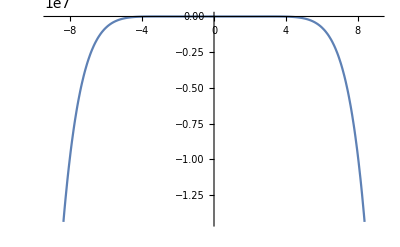

```mathematica
Plot[1.4642136259047618+0.9811989333333337 t^2-4.6198000000000015 t^4+10.156500000000001 t^6-(3303 t^8)/4480,{t,-9.091433821863836,9.091433821863836}]
```

```mathematica
Plot3D[f[z,t],{z,-8,8},{t,-8,8},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[%107,{z,-8,8}],{t,-8,8}]
```

No solution present => power series method not applicable